# Orthogonal Faces for the Tsirelson point

### Basics: states and measurements

One can define operators acting on the single-qubit space as

```mathematica
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
I2=IdentityMatrix[2];
```

and operators acting on the 2-qubit space using the tensor product of single-qubit operators as

```mathematica
ZA=KroneckerProduct[Z,I2];
ZB=KroneckerProduct[I2,Z];
XA=KroneckerProduct[X,I2];
XB=KroneckerProduct[I2,X];
ZZ=KroneckerProduct[Z,Z];
XX=KroneckerProduct[X,X];
ZX=KroneckerProduct[Z,X];
XZ=KroneckerProduct[X,Z];
II=KroneckerProduct[I2,I2];
```

### General parametrization of the Bell expression

It is not clear how a Bell expression can be generically constructed to self-test an arbitrary state. We then consider conditions on Bell expressions that are only necessary for self-testing the state: in particular, one such necessary condition is that the maximal value of a Bell expression has to be achieved by measuring the state.

Depending on the actual measurement operations, a Bell operator can correspond to various Bell expressions. Let us consider the realization:

```mathematica
phiPlus=1/Sqrt[2] {1,0,0,1};
A[i_]:=(ZA+(-1)^i XA)/Sqrt[2] ;
B[0]=ZB;
B[1]=XB;
```

### Tsirelson behavior

Such realization gives the following probability distribution (behavior)

```mathematica
Ops={{II, B[0],B[1]},{A[0],A[0].B[0],A[0].B[1]},{A[1],A[1].B[0],A[1].B[1]}};
Pprime = Table[FullSimplify[ConjugateTranspose[phiPlus].Ops[[i,j]].phiPlus],{i,1,3},{j,1,3}];
Pprime //TableForm
```

1 | 0 | 0
0 | 1/(√2) | 1/(√2)
0 | 1/(√2) | -1/(√2)

Thus the Tsirelson point, expressed as a vector in $\mathbb{R}^8$, reads

```mathematica
PT=Drop[Flatten[Pprime],1];
PT //MatrixForm
```

(0
0
0
1/(√2)
1/(√2)
0
1/(√2)
-1/(√2))

### Parametrizing the general Bell expression

All possible Bell expressions can be parametrized by eight real coefficients and be written in terms of formal polynomials as

```mathematica
(*Formal polynomial*)
BellExpression[A_, B_]:= a[0]A[0]+a[1]A[1]+b[0]B[0]+b[1]B[1]+c[0,0]A[0]B[0]+c[1,0]A[1]B[0]+c[0,1]A[0]B[1]+c[1,1]A[1]B[1];
```

Now consider the expressions of the measurements operators in terms of formal indeterminates:

```mathematica
Clear[A,B];
```

```mathematica
(*Formal polynomials*)
A[i_]:=(ZAA+(-1)^i XAA)/Sqrt[2] ;
B[0]=ZBB;
B[1]=XBB;
```

Or, in terms of X and Z operator indeterminates,

```mathematica
(*Formal polynomial*)
poly =BellExpression[A,B]
```

((XAA+ZAA) a[0])/(√2)+((-XAA+ZAA) a[1])/(√2)+ZBB b[0]+XBB b[1]+((XAA+ZAA) ZBB c[0,0])/(√2)+(XBB (XAA+ZAA) c[0,1])/(√2)+((-XAA+ZAA) ZBB c[1,0])/(√2)+(XBB (-XAA+ZAA) c[1,1])/(√2)

We collect the coefficients of the X and Z expansion:

```mathematica
coeffList =Flatten[CoefficientList[poly,{XAA,XBB,ZAA,ZBB}]]
```

{0,b[0],a[0]/(√2)+a[1]/(√2),c[0,0]/(√2)+c[1,0]/(√2),b[1],0,c[0,1]/(√2)+c[1,1]/(√2),0,a[0]/(√2)-a[1]/(√2),c[0,0]/(√2)-c[1,0]/(√2),0,0,c[0,1]/(√2)-c[1,1]/(√2),0,0,0}

### The Bell operator

Now, consider the Bell operator corresponding to these polynomials for the quantum realization under analysis. A general parametrization is

```mathematica
(*Formal polynomial*)
Sop = p[1]ZAA+p[2]XAA+p[3]ZBB+p[4]XBB+p[5]ZAA ZBB+p[6]XAA XBB+p[7]ZAA XBB+p[8]XAA ZBB;
```

Again, we collect the coefficients of the X and Z expansion:

```mathematica
coeffList2 =Flatten[CoefficientList[Sop,{XAA,XBB,ZAA,ZBB}]]
```

{0,p[3],p[1],p[5],p[4],0,p[7],0,p[2],p[8],0,0,p[6],0,0,0}

The p[i] parameters are linear combinations of parameters a[i], b[i], c[i,j]. In fact,

```mathematica
Psol=Solve[Thread[coeffList==coeffList2],{p[1],p[2],p[3],p[4],p[5],p[6],p[7],p[8]}][[1]]
```

{p[1]→1/2 (√2 a[0]+√2 a[1]),p[2]→1/2 (√2 a[0]-√2 a[1]),p[3]→b[0],p[4]→b[1],p[5]→1/2 (√2 c[0,0]+√2 c[1,0]),p[6]→1/2 (√2 c[0,1]-√2 c[1,1]),p[7]→1/2 (√2 c[0,1]+√2 c[1,1]),p[8]→1/2 (√2 c[0,0]-√2 c[1,0])}

For the Tsirelson behavior, the system is invertible! In fact,

```mathematica
Asols=Solve[Thread[coeffList==coeffList2],{a[0],a[1],b[0],b[1],c[0,0],c[1,0],c[0,1],c[1,1]}][[1]]
```

{a[0]→p[1]/(√2)+p[2]/(√2),a[1]→1/2 (√2 p[1]-√2 p[2]),b[0]→p[3],b[1]→p[4],c[0,0]→p[5]/(√2)+p[8]/(√2),c[1,0]→1/2 (√2 p[5]-√2 p[8]),c[0,1]→p[6]/(√2)+p[7]/(√2),c[1,1]→1/2 (-√2 p[6]+√2 p[7])}

### Conditions on the Bell operator

Now, we want phiPlus to be an eigenstate of S with eigenvalue 1. So we implement the operator in matrix form.

```mathematica
S = p[1] ZA + p[2] XA + p[3] ZB + p[4] XB + p[5] ZZ + p[6] XX + p[7] ZX + p[8] XZ;
```

Now, we compute the action of the Bell operator S (in matrix form) on phiPlus and get some relations between the p[i]s

```mathematica
conditionsList=Thread[S.phiPlus==phiPlus]//FullSimplify//Reduce
```

p[7]==p[8]&&p[2]==-p[4]&&p[5]==1-p[6]&&p[1]==-p[3]

### Reduction of the parameter space

We can rewrite the Bell operator in the indeterminates space:

```mathematica
(*Formal polynomials*)
Spoly =Sop/.{p[8]->p[7],p[4]->-p[2],p[6]->1-p[5],p[3]->-p[1]}
```

ZAA p[1]-ZBB p[1]+XAA p[2]-XBB p[2]+XAA XBB (1-p[5])+ZAA ZBB p[5]+XBB ZAA p[7]+XAA ZBB p[7]

We can now express the Pauli operators in terms of the measurement operators:

```mathematica
Clear[A,B];
solutions = Solve[{A[0]==1/Sqrt[2](ZAA+XAA),A[1]==1/Sqrt[2](ZAA-XAA),B[0]==ZBB,B[1]==XBB},{XAA,XBB,ZAA,ZBB}][[1]]//FullSimplify
```

{XAA→(A[0]-A[1])/(√2),XBB→B[1],ZAA→(A[0]+A[1])/(√2),ZBB→B[0]}

Now, it is natural to re-parametrize the Bell operator as

```mathematica
Spoly/.solutions
```

((A[0]+A[1]) p[1])/(√2)-B[0] p[1]+((A[0]-A[1]) p[2])/(√2)-B[1] p[2]+((A[0]-A[1]) B[1] (1-p[5]))/(√2)+((A[0]+A[1]) B[0] p[5])/(√2)+((A[0]-A[1]) B[0] p[7])/(√2)+((A[0]+A[1]) B[1] p[7])/(√2)

Let us call p[1] = r[0], p[2] = r[1], p[7] = r[2], p[5] = \lambda.

### Re-parametrize the Bell expression

The new parametrization in terms of four parameters reads

```mathematica
Clear[A,B];
```

```mathematica
reducedBell[A_,B_]:=r[0]((A[0]+A[1])/Sqrt[2]-B[0])+r[1]((A[0]-A[1])/Sqrt[2]-B[1])+r[2]((A[0]+A[1])/Sqrt[2] B[1]+(A[0]-A[1])/Sqrt[2] B[0])+λ (A[0]+A[1])/Sqrt[2] B[0]+(1-λ)(A[0]-A[1])/Sqrt[2] B[1];
```

### Variational constraints

In full generality, consider the realization

```mathematica
phi[θ_]:= {Cos[θ],0,0,Sin[θ]};
$Assumptions=θ∈Reals;
A[i_]:=Cos[a[i]]ZA+Sin[a[i]]XA;
B[i_]:=Cos[b[i]]ZB+Sin[b[i]]XB;
```

```mathematica
Ops={{II, B[0],B[1]},{A[0],A[0].B[0],A[0].B[1]},{A[1],A[1].B[0],A[1].B[1]}};
```

The parametrized behavior reads

```mathematica
Ptprime[θ_] := Table[FullSimplify[ConjugateTranspose[phi[θ]].Ops[[i,j]].phi[θ]],{i,1,3},{j,1,3}];
Ptprime[θ] //TableForm
```

1 | Cos[2 θ] Cos[b[0]] | Cos[2 θ] Cos[b[1]]
Cos[2 θ] Cos[a[0]] | Cos[a[0]] Cos[b[0]]+Sin[2 θ] Sin[a[0]] Sin[b[0]] | Cos[a[0]] Cos[b[1]]+Sin[2 θ] Sin[a[0]] Sin[b[1]]
Cos[2 θ] Cos[a[1]] | Cos[a[1]] Cos[b[0]]+Sin[2 θ] Sin[a[1]] Sin[b[0]] | Cos[a[1]] Cos[b[1]]+Sin[2 θ] Sin[a[1]] Sin[b[1]]

```mathematica
Pt[θ_]:=Drop[Flatten[Ptprime[θ]],1];
Pt[θ]//MatrixForm
```

(Cos[2 θ] Cos[b[0]]
Cos[2 θ] Cos[b[1]]
Cos[2 θ] Cos[a[0]]
Cos[a[0]] Cos[b[0]]+Sin[2 θ] Sin[a[0]] Sin[b[0]]
Cos[a[0]] Cos[b[1]]+Sin[2 θ] Sin[a[0]] Sin[b[1]]
Cos[2 θ] Cos[a[1]]
Cos[a[1]] Cos[b[0]]+Sin[2 θ] Sin[a[1]] Sin[b[0]]
Cos[a[1]] Cos[b[1]]+Sin[2 θ] Sin[a[1]] Sin[b[1]])

We write the Bell expression as a vector in $\mathbb{R}^8$:

```mathematica
reducedBell[AA,BB]//FullSimplify//Expand
```

(λ AA[0] BB[0])/(√2)+(λ AA[1] BB[0])/(√2)+(AA[0] BB[1])/(√2)-(λ AA[0] BB[1])/(√2)-(AA[1] BB[1])/(√2)+(λ AA[1] BB[1])/(√2)+(AA[0] r[0])/(√2)+(AA[1] r[0])/(√2)-BB[0] r[0]+(AA[0] r[1])/(√2)-(AA[1] r[1])/(√2)-BB[1] r[1]+(AA[0] BB[0] r[2])/(√2)-(AA[1] BB[0] r[2])/(√2)+(AA[0] BB[1] r[2])/(√2)+(AA[1] BB[1] r[2])/(√2)

The right ordering is (B0, B1, A0, A0B0, A0B1, A1, A1B0, A1B1)

```mathematica
β={-r[0],-r[1],(r[0]+r[1])/Sqrt[2],(r[2]+λ)/Sqrt[2],(1+r[2]-λ)/Sqrt[2],(r[0]-r[1])/Sqrt[2],(λ-r[2])/Sqrt[2],(r[2]+λ-1)/Sqrt[2]}
```

{-r[0],-r[1],(r[0]+r[1])/(√2),(λ+r[2])/(√2),(1-λ+r[2])/(√2),(r[0]-r[1])/(√2),(λ-r[2])/(√2),(-1+λ+r[2])/(√2)}

We can now implement the variational conditions

```mathematica
Da0Pt[θ_]:=D[Pt[θ],a[0]];
Db0Pt[θ_]:=D[Pt[θ],b[0]];
Da1Pt[θ_]:=D[Pt[θ],a[1]];
Db1Pt[θ_]:=D[Pt[θ],b[1]];
DthetaPt[θ_]:=D[Pt[θ],θ];
```

```mathematica
eqa0 = Transpose[β].Da0Pt[θ]==0;
eqb0 = Transpose[β].Db0Pt[θ]==0;
eqa1 = Transpose[β].Da1Pt[θ]==0;
eqb1 = Transpose[β].Db1Pt[θ]==0;
eqtheta = Transpose[β].DthetaPt[θ]==0;
```

We then have to substitute the values of the Tsirelson point:

```mathematica
θ=π/4;
a[0]=0;
a[1]=π/2;
b[i_]:=(-1)^i π/4;
```

```mathematica
Reduce[{eqa0, eqb0, eqa1, eqb1, eqtheta}, {r[0],r[1],r[2],λ}]
```

r[2]==0&&λ==1/2

I got the same results of the paper!

The search space for the Bell inequalities is thus reduced to

```mathematica
reducedBell[AA,BB]/.{r[2]->0,λ->1/2}
```

((AA[0]+AA[1]) BB[0])/(2 √2)+((AA[0]-AA[1]) BB[1])/(2 √2)+((AA[0]+AA[1])/(√2)-BB[0]) r[0]+((AA[0]-AA[1])/(√2)-BB[1]) r[1]

We can write the corresponding vector in $\mathbb{R}^8$. The right ordering is (B0, B1, A0, A0B0, A0B1, A1, A1B0, A1B1)

```mathematica
βred:=β/.{r[2]->0, λ->1/2}
βred //MatrixForm
```

(-r[0]
-r[1]
(r[0]+r[1])/(√2)
1/(2 √2)
1/(2 √2)
(r[0]-r[1])/(√2)
1/(2 √2)
-1/(2 √2))

### Local bounds

The local maxima of a Bell expression is reached at one of the 16 extremal points of the local polytope. This points are given by

```mathematica
OpsL={{1, i,j},{k,i k,j k},{l,i l,j l}};
Lprime[i_,j_,k_,l_] = Table[FullSimplify[OpsL[[a,b]]],{a,1,3},{b,1,3}];
L[i_,j_,k_,l_]:=Drop[Flatten[Lprime[i,j,k,l] ],1];
L[i,j,k,l] //MatrixForm
```

(i
j
k
i k
j k
l
i l
j l)

The convex region of expressions \beta(r0, r1) with a local maximum smaller than 1 is thus given by all points (r0, r1) satisfying \beta \cdot L \eq 1.

```mathematica
ineqs=Flatten[Table[βred.L[i,j,k,l]<=1,{i,{-1,1}},{j,{-1,1}},{k,{-1,1}},{l,{-1,1}}]];
solution=Reduce[ineqs,{r[0],r[1]},Reals]
```

(r[0]==1/2 (-2+√2)&&r[1]==0)||(1/2 (-2+√2)<r[0]≤(-2+√2)/(2 √2)&&(-2+√2-2 r[0])/(-2+2 √2)≤r[1]≤(2-√2+2 r[0])/(-2+2 √2))||((-2+√2)/(2 √2)<r[0]≤0&&1/2 (-2+√2+2 r[0]-2 √2 r[0])≤r[1]≤1/2 (2-√2-2 r[0]+2 √2 r[0]))||(0<r[0]≤(2-√2)/(2 √2)&&1/2 (-2+√2-2 r[0]+2 √2 r[0])≤r[1]≤1/2 (2-√2+2 r[0]-2 √2 r[0]))||((2-√2)/(2 √2)<r[0]<1/2 (2-√2)&&(-2+√2+2 r[0])/(-2+2 √2)≤r[1]≤(2-√2-2 r[0])/(-2+2 √2))||(r[0]==1/2 (2-√2)&&r[1]==0)

The intersection of these half-planes defines a polytope, namely an octagon in the (r0, r1) plane.

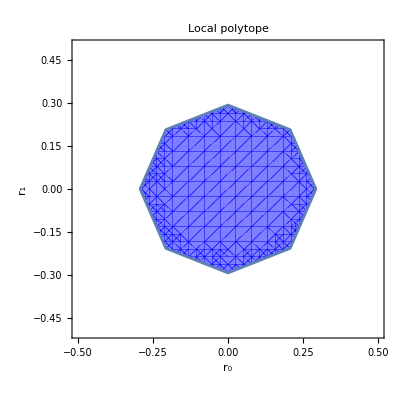

```mathematica
RegionPlot[solution,{r[0],-0.5,0.5},{r[1],-0.5,0.5},
PlotStyle->Directive[Opacity[0.5],Blue],
AxesLabel->{Style["r₀",Bold,14],Style["r₁",Bold,14]},
PlotLabel->Style["Local polytope",Bold,16],
PlotLegends->"Expressions"]
```

Any Bell expression outside this octagon has a local bound larger than 1, and thus is not maximized by the Tsirelson behavior.

### Quantum bounds

Having excluded a range of Bell expressions $\beta_{r_0 ,r_1}$ from their local bound, we need to compute the Tsirelson bound (quantum bound) of the expressions inside the octagon.

Let us consider the algebra of quantum operators $R$ made of arbitrary products of $A_x$ and $B_y$. The only generating rules of this algebra are that, for all x,y,  $A_x^2= B_y^2= 1$ (they are projectors) and [A_x, B_y] = 0. We know that a sufficient condition to have $\beta ⪯1$ is that $1−\beta$ is a sum of squares (SOS) in R (SOS relaxation). However, the search space $R$ is of infinite dimension.

A common approach to tackle this problem consists in considering operators $O_s$ within a chosen relaxation level T, such as the set of all polynomials of $A_x$ and $B_y$ of a given degree. But even this quickly results in a large problem.

It is easy to show that the operators of the SOS expression should be nullifiers of phiPlus! Given a basis of nullifiers \vec{N}, then one can show that 

1 - β = N^\dagger. W3.N

where W3 is a positive matrix.If such a matrix W3 can be found, we say it is a certificate of the inequality β.

Different relaxations could be considered:

1) The first order relaxation T_{1+A+B} = \{1, A_0, A_1, B_0, B_1\}$ only gives a certificate for the CHSH inequality. 

2) The relaxation at the almost quantum level, T_(1+A+B+AB) can also be computed numerically and gives a certificate for a disk in the $(r_0, r_1)$ plane of center (0,0) and radius 1/(4Sqrt[2]).

### SOS relaxation at level T_(1+A+B+AB+ABB') for the inequality β_T

3) The next relaxation is given by T_(1+A+B+AB+ABB)

We can show analytically that a certificate can be found for the inequality $\beta_{1−1/Sqrt[2], 0} at this level of relaxation. This ensures that the Bell expression $\beta_{1-1/Sqrt[2],0}$ is maximized by the Tsirelson point.

One can choose the following basis of Nullifiers:

```mathematica
Clear[A,B];
```

```mathematica
NN[A_,B_]= {(A[0]+A[1])/Sqrt[2]-B[0], (A[0]-A[1])/Sqrt[2]-B[1],1-(A[0]+A[1])/Sqrt[2] B[0],1-(A[0]-A[1])/Sqrt[2] B[1],(A[0]+A[1])/Sqrt[2] B[1]+(A[0]-A[1])/Sqrt[2] B[0],B[1](1-(A[0]+A[1])/Sqrt[2] B[0]),B[0](1-(A[0]-A[1])/Sqrt[2] B[1]),(1+(A[0]+A[1])/Sqrt[2] B[0])B[1],(1+(A[0]-A[1])/Sqrt[2] B[1])B[0]};
NN[A,B]//MatrixForm
```

((A[0]+A[1])/(√2)-B[0]
(A[0]-A[1])/(√2)-B[1]
1-((A[0]+A[1]) B[0])/(√2)
1-((A[0]-A[1]) B[1])/(√2)
((A[0]-A[1]) B[0])/(√2)+((A[0]+A[1]) B[1])/(√2)
(1-((A[0]+A[1]) B[0])/(√2)) B[1]
B[0] (1-((A[0]-A[1]) B[1])/(√2))
(1+((A[0]+A[1]) B[0])/(√2)) B[1]
B[0] (1+((A[0]-A[1]) B[1])/(√2)))

Then, we call V the following 6-vector of nullifiers (notice the ordering)

```mathematica
V = {NN[A,B][[1]],NN[A,B][[3]],NN[A,B][[7]],NN[A,B][[2]],NN[A,B][[6]],NN[A,B][[5]]};
```

```mathematica
V//MatrixForm
```

((A[0]+A[1])/(√2)-B[0]
1-((A[0]+A[1]) B[0])/(√2)
B[0] (1-((A[0]-A[1]) B[1])/(√2))
(A[0]-A[1])/(√2)-B[1]
(1-((A[0]+A[1]) B[0])/(√2)) B[1]
((A[0]-A[1]) B[0])/(√2)+((A[0]+A[1]) B[1])/(√2))

We will prove that a certificate is provided by the following matrix W:

```mathematica
s = 2 - Sqrt[2];
W = 1/16{{Sqrt[2],-2s, -s, 0, 0, 0},{-2s, 2s, 0, 0, 0, 0},{-s,0,Sqrt[2],0,0,0},{0,0,0,2,0,s},{0,0,0,0,s Sqrt[2],s},{0,0,0,s,s,s}};
W//MatrixForm
```

(1/(8 √2) | 1/8 (-2+√2) | 1/16 (-2+√2) | 0 | 0 | 0
1/8 (-2+√2) | 1/8 (2-√2) | 0 | 0 | 0 | 0
1/16 (-2+√2) | 0 | 1/(8 √2) | 0 | 0 | 0
0 | 0 | 0 | 1/8 | 0 | 1/16 (2-√2)
0 | 0 | 0 | 0 | (2-√2)/(8 √2) | 1/16 (2-√2)
0 | 0 | 0 | 1/16 (2-√2) | 1/16 (2-√2) | 1/16 (2-√2))

We calculate V^\dagger W V:

```mathematica
Collect[Expand[FullSimplify[Transpose[V].W.V]],{A[0],B[0],A[1],B[1]}]
```

1/4-1/(4 √2)+B[1]^2/(4 √2)+A[1] (1/4-1/(2 √2)+B[1]/(4 √2))+A[1]^2 (1/16+1/(16 √2)+(-1/8+1/(8 √2)) B[1]+(1/16-1/(16 √2)) B[1]^2)+B[0]^2 (1/4+A[1] (1/4-1/(2 √2)+B[1]/(4 √2))+A[1]^2 (3/16-3/(16 √2)+(1/8-1/(8 √2)) B[1]+(-1/16+3/(16 √2)) B[1]^2))+A[0]^2 (1/16+1/(16 √2)+(1/8-1/(8 √2)) B[1]+(1/16-1/(16 √2)) B[1]^2+B[0] (3/8-3/(8 √2)+(1/4-1/(4 √2)) B[1]+(-1/8+1/(8 √2)) B[1]^2)+B[0]^2 (3/16-3/(16 √2)+(-1/8+1/(8 √2)) B[1]+(-1/16+3/(16 √2)) B[1]^2))+B[0] (1/2-1/(2 √2)+A[1]^2 (3/8-3/(8 √2)+(-1/4+1/(4 √2)) B[1]+(-1/8+1/(8 √2)) B[1]^2)+A[1] (1/4-3/(4 √2)+(-1/4+1/(4 √2)) B[1]^2))+A[0] (1/4-1/(2 √2)-B[1]/(4 √2)+A[1] (-1/8+1/(8 √2)+(1/8-1/(8 √2)) B[1]^2)+B[0]^2 (1/4-1/(2 √2)-B[1]/(4 √2)+A[1] (1/8-1/(8 √2)+(-1/8+1/(8 √2)) B[1]^2))+B[0] (1/4-3/(4 √2)+(-1/4+1/(4 √2)) B[1]^2+A[1] (1/4-1/(4 √2)+(-1/4+1/(4 √2)) B[1]^2)))

For r_0 = 1 - 1/Sqrt[2], r_1 = 0, the Bell expression is

```mathematica
βf=reducedBell[A,B]/.{r[0]->1-1/Sqrt[2],r[1]->0,r[2]->0, λ->1/2}
```

(1-1/(√2)) ((A[0]+A[1])/(√2)-B[0])+((A[0]+A[1]) B[0])/(2 √2)+((A[0]-A[1]) B[1])/(2 √2)

Substituting everything in the equation 1 - β(r_0, r_1) = V^\dagger W V, and imposing A^2 = B^2 = 1, we get

```mathematica
eq =FullSimplify[1 -βf==Transpose[V].W.V]/.{A[0]^2->1,A[1]^2->1,B[0]^2->1,B[1]^2->1}//FullSimplify
```

8 B[0]^2+(2+√2) B[1]^2+4 (-2+√2) B[0] (-1+B[1]^2)==10+√2

```mathematica
eq/.{B[0]^2->1,B[1]^2->1}//FullSimplify
```

True

We can also verify that the matrix W has four non-negative eigenvalues:

```mathematica
W //Eigenvalues
```

{1/8 (1+√(10-7 √2)),1/16 (-2+3 √2),1/8 (1-√(10-7 √2)),1/8 (2-√2),0,0}

### Changing notation

We change notation to implement with a Python code the NPA hierarchy:

```mathematica
Clear[A,B];
```

```mathematica
reducedBell[AA,BB]/.{r[2]->0,λ->1/2}
```

((AA[0]+AA[1]) BB[0])/(2 √2)+((AA[0]-AA[1]) BB[1])/(2 √2)+((AA[0]+AA[1])/(√2)-BB[0]) r[0]+((AA[0]-AA[1])/(√2)-BB[1]) r[1]

```mathematica
AA[i_]:= 2A[0,i]-1;
BB[i_]:=2B[0,i]-1;
```

```mathematica
reducedBell[AA,BB]/.{r[2]->0,λ->1/2}//FullSimplify//Expand
```

1/(√2)-√2 A[0,0]-√2 B[0,0]+√2 A[0,0] B[0,0]+√2 A[0,1] B[0,0]+√2 A[0,0] B[0,1]-√2 A[0,1] B[0,1]+r[0]-√2 r[0]+√2 A[0,0] r[0]+√2 A[0,1] r[0]-2 B[0,0] r[0]+r[1]+√2 A[0,0] r[1]-√2 A[0,1] r[1]-2 B[0,1] r[1]